#### Analytical

```mathematica
FourierTransform[Exp[-t^2],t,w,FourierParameters->{1, -1}]
```

ⅇ^(-w^2/4) √π

#### Calculations

```mathematica
f[t_]:=Exp[-t^2]
F[w_]:=Exp[-w^2/4]*Sqrt[Pi]
```

```mathematica
fexcp[tMax_,dt_]:=Module[{tSamples,n,wSamples,fSamples},
tSamples=Table[f[t]//N,{t,-tMax,tMax,dt}];

n=Length[tSamples];
wSamples=Range[-n/2,n/2-dt,1]/n/dt*2Pi//N;
fSamples=Fourier[tSamples*dt*Sqrt[n]*Table[(-1)^(m-1),{m,1,Length[tSamples]}]];

Transpose[{wSamples,Abs/@fSamples}]
]
```

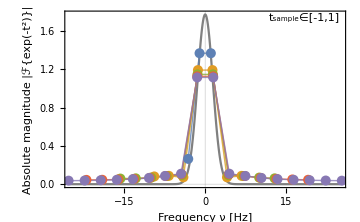

```mathematica
g1=Show[{

Plot[F[w],{w,-25,25},PlotRange->All,ImageSize->Medium,PlotStyle->Gray],

ListLinePlot[Evaluate[Table[fexcp[1,1/d],{d,1,10,2}]],PlotRange->All,PlotStyle->(Directive[{Opacity[0.8],Thin,ColorData[97]@#}]&/@Range[1,5])],
ListPlot[Evaluate[Table[fexcp[1,1/d],{d,1,10,2}]],PlotRange->All,PlotStyle->(Directive[{ColorData[97]@#,PointSize[0.02]}]&/@Range[1,5])]

},
PlotRange->{{-25,25},All},
FrameLabel->Thread[Style[{"Frequency ν [Hz]","Absolute magnitude |ℱ{exp(-t^2)}|"},FontSize->16]],
Epilog->{Inset[Grid[{{LineLegend[{Gray},{Style["Analyt.",{FontSize->14,FontColor->GrayLevel[0.2]}]}]},{Style["t_sample∈[-1,1]",{FontSize->14,FontColor->GrayLevel[0.2]}]},{PointLegend[ColorData[97]/@Range[1,5],Style[#,{FontSize->14,FontColor->GrayLevel[0.2]}]&/@{"Δt = 1","Δt = 1/3","Δt = 1/5","Δt = 1/7","Δt = 1/9"}]}}],{25,1.8},{Right,Top}]}]
```

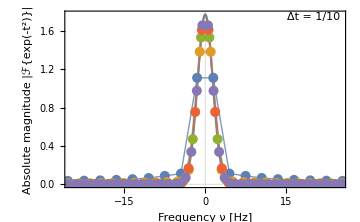

```mathematica
g2=Show[{

Plot[F[w],{w,-25,25},PlotRange->All,ImageSize->Medium,PlotStyle->Gray],

ListLinePlot[Evaluate[Table[fexcp[d,1/10],{d,1,3,1/2}]],PlotRange->All,PlotStyle->(Directive[{Opacity[0.8],Thin,ColorData[97]@#}]&/@Range[1,5])],
ListPlot[Evaluate[Table[fexcp[d,1/10],{d,1,3,1/2}]],PlotRange->All,PlotStyle->(Directive[{ColorData[97]@#,PointSize[0.02]}]&/@Range[1,5])]

},
PlotRange->{{-25,25},All},
FrameLabel->Thread[Style[{"Frequency ν [Hz]","Absolute magnitude |ℱ{exp(-t^2)}|"},FontSize->16]],
Epilog->{Inset[Grid[{{LineLegend[{Gray},{Style["Analyt.",{FontSize->14,FontColor->GrayLevel[0.2]}]}]},{Style["Δt = 1/10",{FontSize->14,FontColor->GrayLevel[0.2]}]},{PointLegend[ColorData[97]/@Range[1,5],Style[#,{FontSize->14,FontColor->GrayLevel[0.2]}]&/@{"t_smpl∈[-1,1]","t_smpl∈[-1.5,1.5]","t_smpl∈[-2,2]","t_smpl∈[-2.5,2.5]","t_smpl∈[-3,3]"}]}}],{25,1.8},{Right,Top}]}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DT_Comparison.pdf"}],g1]
Export[FileNameJoin[{NotebookDirectory[],"TSampling_Comparison.pdf"}],g2]
```

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_01\A2\data\DT_Comparison.pdf

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_01\A2\data\TSampling_Comparison.pdf

#### ContourSampling

```mathematica
fexcpError[tMax_,dt_]:=Module[{tSamples,n,wSamples,fSamples,fAnaSamples},
tSamples=Table[f[t]//N,{t,-tMax,tMax,dt}];

n=Length[tSamples];
wSamples=Range[-n/2,n/2-dt,1]/n/dt*2Pi//N;
fSamples=Abs/@Fourier[tSamples*dt*Sqrt[n]*Table[(-1)^(m-1),{m,1,Length[tSamples]}]];
fAnaSamples=Table[F[w]//N,{w,wSamples}];

Total[Abs[fAnaSamples-fSamples]^2]
]
```

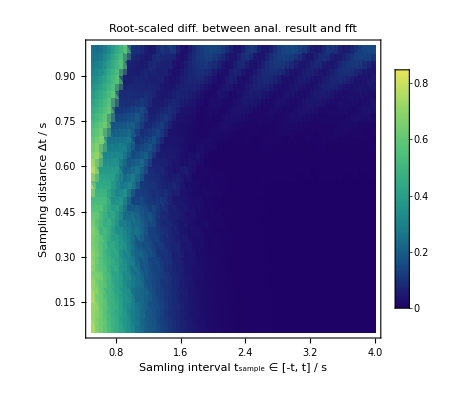

```mathematica
g3=ListDensityPlot[Flatten[Table[{tm,dtm,Sqrt@fexcpError[tm,dtm]}//N,{tm,1/2,4,1/20},{dtm,1/20,1,1/40}],1],PlotLegends->Automatic,PlotRange->All,ColorFunction->"BlueGreenYellow",FrameLabel->Thread[Style[{"Samling interval t_sample ∈ [-t, t]  /  s","Sampling distance Δt  /  s"},FontSize->16]],PlotLabel->Style["Root-scaled diff. between anal. result and fft",FontSize->16]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"DT_TSampling_Contour.png"}],g3]
```

C:\Users\Jelle\Desktop\coding\ComputationalPhotonics\Excercise_01\A2\DT_TSampling_Contour.png